```mathematica
(* Detecting nonlocality in spin-nematic squeezed states as prepared in a spin-1 BEC *)
Needs["SUN`"]; (* https://github.com/kercl/sun *)
Needs["MaTeX`"];
texStyle={FontFamily->"Latin Modern Roman",FontSize->15};
```

```mathematica
(* Max violation qutrits *)
P00Il=DiagonalMatrix[{1,0,0}];
P10Il=DiagonalMatrix[{0,1,0}];
P01Il = {{1/4,-1/4,1/(2 √2)},{-1/4,1/4,-1/(2 √2)},{1/(2 √2),-1/(2 √2),1/2}};
P11Il = {{1/4,-1/4,-1/(2 √2)},{-1/4,1/4,1/(2 √2)},{-1/(2 √2),1/(2 √2),1/2}};
P01Il // MatrixForm 
P11Il // MatrixForm
```

(1/4 | -1/4 | 1/(2 √2)
-1/4 | 1/4 | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/2)

(1/4 | -1/4 | -1/(2 √2)
-1/4 | 1/4 | 1/(2 √2)
-1/(2 √2) | 1/(2 √2) | 1/2)

```mathematica
Eigenvalues[P01Il]
Eigenvectors[P01Il]
Eigenvalues[P11Il]
Eigenvectors[P11Il]
```

{1,0,0}

{{1/(√2),-1/(√2),1},{-√2,0,1},{1,1,0}}

{1,0,0}

{{-1/(√2),1/(√2),1},{√2,0,1},{1,1,0}}

```mathematica
(* Max violation qubits *)
P00B=DiagonalMatrix[{1,0,0}];
P10B=DiagonalMatrix[{0,1,0}];
P01B = DiagonalMatrix[{0,1,0}];
P11B = {{1/2,0,(√3)/2}}†.{{1/2,0,(√3)/2}};
```

```mathematica
bF3[P00_,P10_,P01_,P11_]:=  (Ir[P00]-Ir[P11]). (Ir[P00]-Ir[P11]) + (Ir[P01]-Ir[P10]). (Ir[P01]-Ir[P10]) + Ir[P00.P11 + P11.P00] + Ir[P01.P10 + P10.P01]
```

```mathematica
Min[Eigenvalues[N[bF3[P00B, P10B, P01B, P11B]]]]
Min[Eigenvalues[N[bF3[P00Il, P10Il, P01Il, P11Il]]]]
```

-0.25

-0.5

```mathematica
MatGM=LieAlgebraBasisMatrices[Irrep[1,0]][[1]];
```

```mathematica
bounds[Np_]:={
dim=Dimensions[MatSU3][[2]];
MatSU3=LieAlgebraBasisMatrices[Irrep[Np,0]][[1]];
dim=Dimensions[MatSU3][[2]];
Ir[A_]:=Sum[2*Tr[A.MatGM[[a]]]*MatSU3[[a]],{a,1,8}]+Np*Tr[A]*IdentityMatrix[dim, SparseArray]/3;
BF3[P00_,P10_,P01_,P11_]:= (Ir[P00]-Ir[P11]). (Ir[P00]-Ir[P11]) + (Ir[P01]-Ir[P10]). (Ir[P01]-Ir[P10]) + Ir[P00.P11 + P11.P00] + Ir[P01.P10 + P10.P01],
Min[Eigenvalues[N[BF3[P00B, P10B, P01B, P11B]]]]/Np,
Min[Eigenvalues[N[BF3[P00Il, P10Il, P01Il, P11Il]]]]/Np}
```

```mathematica
Npmax = 100;
boundn = Table[bounds[Np][[2;;3]], {Np,1,Npmax}];
```

Eigenvalues::arh: Because finding 105 out of the 105 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

Eigenvalues::arh: Because finding 120 out of the 120 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

```mathematica
(*Export["boundn.dat", boundn];*)
boundn = Import["boundn.dat"];
```

```mathematica
boundn[[32]]*32
```

{-3.70081,-6.78167}

```mathematica
SU2wave = Table[N[-1/4 +(1/(2*n))* (Sqrt[3*n+1]-1)], {n,1,100}];
SU3wave = Table[N[-1/2 -5/(4*n) +(1/n)*(Sqrt[3*n/2+9/16] + Sqrt[n/2+1/4])], {n,1,100}];
```

```mathematica
parties = Table[3i, {i,1,100/3}];
boundnn = Table[boundn[[parties[[i]]]], {i,1,100/3}];
```

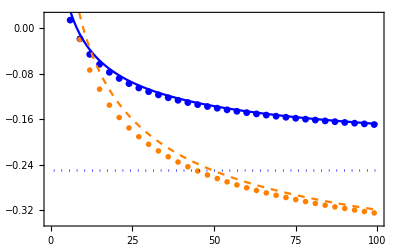

```mathematica
Show[ListPlot[Transpose[{parties, Transpose[boundnn][[1]]}],  PlotLegends->Placed[{MaTeX["\\mbox{qubits}"]},{Right, 0.9}], PlotMarkers->{Graphics[{Disk[]},ImageSize->7]}, PlotStyle->Blue],
ListPlot[Transpose[{parties, Transpose[boundnn][[2]]}],  PlotLegends->Placed[{MaTeX["\\mbox{qutrits}"]},{Right, 0.8}], PlotStyle->{Orange}, PlotMarkers->{"*",20}],
ListLinePlot[SU2wave,PlotStyle-> {Blue}, PlotLegends->Placed[{MaTeX["\\mbox{HP qubits}"]},{Right, 0.7}]],
Plot[{-1/4}, {x,1,100}, PlotStyle->{Dotted, Blue}, PlotLegends->Placed[{MaTeX["\\mbox{qubits bound}"]},{Left, Bottom}]], 
(*Plot[{-1/2}, {x,1,100}, PlotStyle->{DotDashed,Orange}, PlotLegends->Placed[{MaTeX["\mbox{qubits bound}"]},{Left, Bottom}]],*) 
ListLinePlot[SU3wave, PlotStyle->{Orange, Dashed},PlotLegends->Placed[{MaTeX["\\mbox{HP qutrits}"]},{Right, 0.6}]],
FrameLabel->{MaTeX["n", FontSize->18],MaTeX["<\\hat{\\mathcal{B}}>/n", FontSize->15]}, Frame->True,BaseStyle->texStyle, PlotRange->{{0,100},{-0.34, 0.02}}]
```